```mathematica
h = 0.05;
```

```mathematica
beta = 1 + k/20 /. k-> 5;
```

```mathematica
f[x_, y_] := beta + x + y^2
```

```mathematica
eps = 10^(-4);
```

```mathematica
(* Estimating solution interval *)
```

```mathematica
amax = a /. Solve[4*a^3+4*beta*a^2-1==0, a] // Max; {amax, N@amax}
```

{1/8 (-1+√17),0.390388}

```mathematica
bmax = b /. Solve[b == amax * f[amax, b], b] // Max; {bmax, N@bmax}
```

{1/4 (1+√17),1.28078}

```mathematica
(* Exact solution and its plot *)
```

```mathematica
sol = DSolve[{y'[x] == f[x, y[x]], y[0] == 0}, y, x][[1,1,2]]
```

Function[{x},((-1)^(1/3) AiryAiPrime[-(-1)^(1/3) (-5/4-x)] AiryBiPrime[5/4 (-1)^(1/3)]-(-1)^(1/3) AiryAiPrime[5/4 (-1)^(1/3)] AiryBiPrime[-(-1)^(1/3) (-5/4-x)])/(AiryAiPrime[5/4 (-1)^(1/3)] AiryBi[-(-1)^(1/3) (-5/4-x)]-AiryAi[-(-1)^(1/3) (-5/4-x)] AiryBiPrime[5/4 (-1)^(1/3)])]

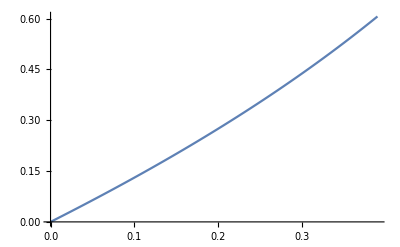

```mathematica
Plot[sol[x], {x, 0, amax}]
```

```mathematica
(* Taylor expansion *)
```

```mathematica
y0max = b /. Solve[2*h * f[2*h, b]== b, b] // Min;
y1max = beta + 2*h + y0max^2;
y2max = 1 + 2* y0max * y1max;
y3max = 2 * (y1max^2 + y0max*y2max);
y4max = 2 * (2*y1max*y2max + y1max*y2max + y0max*y3max);
y5max = 2* (2*(y2max^2 + y1max*y3max) + y2max^2 + 2*y1max*y3max + y0max*y4max);
N[((2*h)^5*y5max/Factorial[5]) / desiredError /. desiredError ->(0.5 * 10^(-5))]
```

0.998106

```mathematica
dy = {beta, 1, 2*beta^2, 6*beta};
```

```mathematica
T = Function[{x}, dy[[1]]*x + dy[[2]]*x^2/2 + dy[[3]]*x^3/6 + dy[[4]]*x^4/24];
```

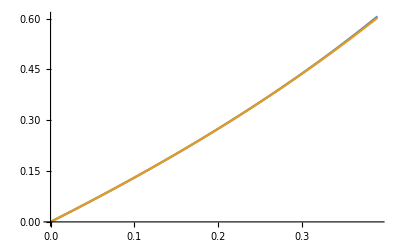

```mathematica
Plot[{sol[x], T[x]}, {x, 0, amax}]
```

```mathematica
xv[i_] := h*i
```

```mathematica
(* Note: "f /@ l" is a shorthand for Map[f, l]. It is right-associative, of course. *)
TaylorVals = T /@ xv /@ Range[-2, 2]
```

{-0.12049,-0.0613132,0.,0.0638171,0.130552}

```mathematica
(* Runge–Kutta *)
```

```mathematica
RungeKuttaStep[f_, xi_, yi_, h_] := Module[{k1, k2, k3, k4},
k1 = h * f[xi, yi];
k2 = h * f[xi + h/2, yi + k1/2];
k3 = h * f[xi + h/2, yi + k2/2];
k4 = h * f[xi + h, yi + k3];
{xi + h, yi + 1/6 * (k1 + 2*k2 + 2*k3 + k4)}
]
```

```mathematica
(* Note: "#" means "first argument". "#1" and "#2" mean 1st and 2nd argument, respectively. "&" means "make the thing on the left a function". *)
RKnumpoints = 2;
RKVals = NestList[RungeKuttaStep[f, #[[1]], #[[2]], h]&, {0, 0}, RKnumpoints]
```

{{0,0},{0.05,0.0638172},{0.1,0.130555}}

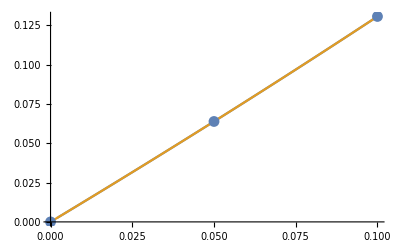

```mathematica
Show[Plot[{sol[x], T[x]}, {x, 0, RKnumpoints*h}], ListPlot[RKVals]]
```

```mathematica
(* Adams *)
```

```mathematica
(* Setting up *)
```

```mathematica
SetAttributes[FillRowDeltas, HoldAll];
FillRowDeltas[array_, rownum_, startcol_, endcol_] :=
Do[
array[[rownum, j]] = array[[rownum - 1, j - 1]] - array[[rownum, j-1]]
, {j, startcol, endcol}];
```

```mathematica
deltas = Table[0, {11}, {6}];
```

```mathematica
MatrixForm[deltas]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Do[
deltas[[i + 3, 1]] = T[xv[i]];
deltas[[i + 3, 2]] = h * f[xv[i], T[xv[i]]];
, {i, -2, 2}]
```

```mathematica
MatrixForm[deltas]
```

(-0.12049 | 0.0582259 | 0 | 0 | 0 | 0
-0.0613132 | 0.060188 | 0 | 0 | 0 | 0
0. | 0.0625 | 0 | 0 | 0 | 0
0.0638171 | 0.0652036 | 0 | 0 | 0 | 0
0.130552 | 0.0683522 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
Do[
Do[
deltas[[i, j]] = deltas[[i - 1, j - 1]] - deltas[[i, j-1]]
, {i, j-1, 5}]
, {j, 3, 6}]
```

```mathematica
MatrixForm[deltas]
```

(-0.12049 | 0.0582259 | 0 | 0 | 0 | 0
-0.0613132 | 0.060188 | -0.00196208 | 0 | 0 | 0
0. | 0.0625 | -0.00231203 | 0.000349957 | 0 | 0
0.0638171 | 0.0652036 | -0.00270363 | 0.000391596 | -0.0000416392 | 0
0.130552 | 0.0683522 | -0.00314856 | 0.000444931 | -0.0000533347 | 0.0000116954
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
AdamsExtrapCoeff[j_] := 1/Factorial[j] * Integrate[Product[t+k, {k,0,j-1}], {t, 0, 1}]
```

```mathematica
AdamsExtrapCoeff /@ Range[0, 4]
```

{1,1/2,5/12,3/8,251/720}

```mathematica
Do[
yi = deltas[[i+2, 1]] + Total[AdamsExtrapCoeff[# - 2] * deltas[[i+2, #]] & /@ Range[2, 6]];
deltas[[i+3, 1]] = yi;
deltas[[i+3, 2]] = h*f[xv[i], yi];
FillRowDeltas[deltas, i+3, 3, 6];
, {i, 3, 5}]
```

```mathematica
MatrixForm[deltas]
```

(-0.12049 | 0.0582259 | 0 | 0 | 0 | 0
-0.0613132 | 0.060188 | -0.00196208 | 0 | 0 | 0
0. | 0.0625 | -0.00231203 | 0.000349957 | 0 | 0
0.0638171 | 0.0652036 | -0.00270363 | 0.000391596 | -0.0000416392 | 0
0.130552 | 0.0683522 | -0.00314856 | 0.000444931 | -0.0000533347 | 0.0000116954
0.197499 | 0.0719503 | -0.00359811 | 0.000449548 | -4.61737×10^-6 | -0.0000487173
0.267819 | 0.0760864 | -0.00413606 | 0.000537948 | -0.0000883996 | 0.0000837822
0.342058 | 0.0808502 | -0.00476382 | 0.000627762 | -0.0000898144 | 1.41481×10^-6
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

```mathematica
AdamsExtrapPoints = {xv[#], deltas[[#+3, 1]]}& /@ Range[-2, 8];
```

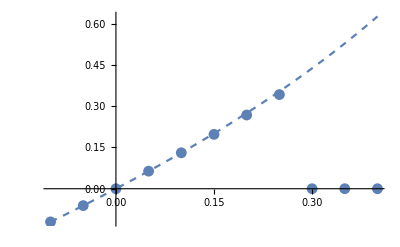

```mathematica
Show[Plot[sol[x], {x, -2*h, 8*h}, PlotStyle->Dashed], ListPlot[AdamsExtrapPoints]]
```

```mathematica
AdamsInterpCoeff[j_] := 1/Factorial[j] * Integrate[Product[t+k, {k,0,j-1}], {t, -1, 0}]
```

```mathematica
AdamsInterpCoeff /@ Range[0, 4]
```

{1,-1/2,-1/12,-1/24,-19/720}

```mathematica
Do[
yi = deltas[[i+2, 1]] + Total[AdamsInterpCoeff[# - 2] * deltas[[i+2, #]]& /@ Range[2, 6]];
While[Abs[yi-deltas[[i+3, 1]]] > eps,
deltas[[i+3, 1]] = yi;
deltas[[i+3, 2]] = h*f[xv[i], yi];
FillRowDeltas[deltas, i+3, 3, 6];
]
, {i, 6, 8}]
```

```mathematica
MatrixForm[deltas]
```

(-0.12049 | 0.0582259 | 0 | 0 | 0 | 0
-0.0613132 | 0.060188 | -0.00196208 | 0 | 0 | 0
0. | 0.0625 | -0.00231203 | 0.000349957 | 0 | 0
0.0638171 | 0.0652036 | -0.00270363 | 0.000391596 | -0.0000416392 | 0
0.130552 | 0.0683522 | -0.00314856 | 0.000444931 | -0.0000533347 | 0.0000116954
0.197499 | 0.0719503 | -0.00359811 | 0.000449548 | -4.61737×10^-6 | -0.0000487173
0.267819 | 0.0760864 | -0.00413606 | 0.000537948 | -0.0000883996 | 0.0000837822
0.342058 | 0.0808502 | -0.00476382 | 0.000627762 | -0.0000898144 | 1.41481×10^-6
0.425241 | 0.0865415 | -0.00569133 | 0.000927511 | -0.000299749 | 0.000209935
0.514558 | 0.0932385 | -0.006697 | 0.00100566 | -0.0000781534 | -0.000221596
0.61107 | 0.10117 | -0.00793185 | 0.00123485 | -0.00022919 | 0.000151037)

```mathematica
AdamsInterpPoints = {xv[#], deltas[[#+3, 1]]}& /@ Range[-2, 8];
```

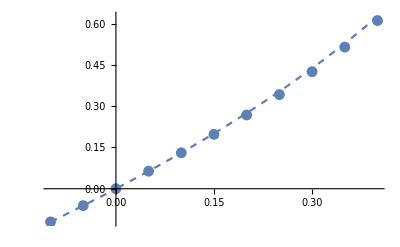

```mathematica
Show[Plot[sol[x], {x, -2*h, 8*h}, PlotStyle->Dashed], ListPlot[AdamsInterpPoints]]
```